Sample integral.
Integral[f[p,u],{p,0,1}] can be expressed analytically as a function of u and is given in the definition “fanalytic”.
But, it is too difficult for symbolic algebra systems such as Mathematica (actually it did it!)
The result is a linear combination of a known set of basis functions (known by theoretical arguments which
use the singularity and branch cut structure of the integral).
So, we could do the integral numerically at a set of values for u, then fit the result.
This can be done by standard fits at some level of precision.
The question is, can we do it at a high enough precision to find the exact coefficients.
Note that they are simple rational numbers times (known) powers of pi and zeta[3].
In another notebook we will show how to fit high precision numerical results to exact expressions.

```mathematica
f[p_,u_] :=(-(1/(24 π^2 (p+u-p u)^2)) (p π^2-2 p π^2 u+π^2 u^2+p π^2 u^2-3 (p (-1+u)^2+u^2) Log[p]^2-24 u Log[(1-u) u]-24 p u Log[(1-u) u]+24 u^2 Log[(1-u) u]+24 p u^2 Log[(1-u) u]-12 p Log[(1-u) u]^2+24 p u Log[(1-u) u]^2-12 u^2 Log[(1-u) u]^2-12 p u^2 Log[(1-u) u]^2+12 Log[p] ((-1-p) (-1+u) u+(p (-1+u)^2+u^2) Log[(1-u) u])-12 (p (-1+u)^2+u^2) PolyLog[2,p])-(1/(24 π^2)) (π^2 (1-2 u+2 u^2)+12 (1-2 u+2 u^2) Log[1-u]^2-48 (-1+u) u Log[u]+12 (1-2 u+2 u^2) Log[u]^2+24 Log[1-u] (-2 (-1+u) u+(1-2 u+2 u^2) Log[u]))) 1/(1-p)
```

```mathematica
fanalytic = Expand[((4-12 u+8 u^2+4 I π (1-3 u+2 u^2)+π^2 (1-2 u+2 u^2)) Log[-1+u])/(4 π^2)+((-2+6 u-4 u^2+I π (1-2 u+2 u^2)) Log[-1+u]^2)/(4 π^2)-((1-2 u+2 u^2) Log[-1+u]^3)/(12 π^2)+((4 I π+4 (1-2 u)^2+π^2 (3-6 u+6 u^2)) Log[u])/(8 π^2)+(I (I+π-2 π u+2 π u^2) Log[-1+u] Log[u])/(2 π^2)-((1-2 u+2 u^2) Log[-1+u]^2 Log[u])/(4 π^2)+((u (-3+2 u)+2 I π (1-2 u+2 u^2)) Log[u]^2)/(2 π^2)+((-1+2 u-2 u^2) Log[-1+u] Log[u]^2)/π^2-((1-2 u+2 u^2) Log[u]^3)/(2 π^2)+((1-2 u) PolyLog[2,1-u])/(2 π^2)+((1-6 u+4 u^2+2 I π (1-2 u+2 u^2)) PolyLog[2,(-1+u)/u])/(4 π^2)-((1-2 u+2 u^2) Log[-1+u] PolyLog[2,(-1+u)/u])/(2 π^2)-((1-2 u+2 u^2) Log[u] PolyLog[2,(-1+u)/u])/(2 π^2)+((1-2 u+2 u^2) Log[u] PolyLog[2,u])/(2 π^2)-((1-2 u+2 u^2) PolyLog[3,(-1+u)/u])/(4 π^2)-((1-2 u+2 u^2) PolyLog[3,u])/(2 π^2)+((1-2 u+2 u^2) PolyLog[3,u/(-1+u)])/(2 π^2)+1/(24 π^2) (-24 I π (1-3 u+2 u^2)-2 I π^3 (1-2 u+2 u^2)+π^2 (11-29 u+18 u^2)-6 (1-2 u+2 u^2) Zeta[3])];
analytic = N[fanalytic]
```

(0.427885-0.580109 ⅈ)-(1.14744-1.47853 ⅈ) u+(0.689103-1.16022 ⅈ) u^2+(0.351321+0.31831 ⅈ) Log[-1.+u]-(0.803964+0.95493 ⅈ) u Log[-1.+u]+(0.702642+0.63662 ⅈ) u^2 Log[-1.+u]-(0.0506606-0.0795775 ⅈ) Log[-1.+u]^2+(0.151982-0.159155 ⅈ) u Log[-1.+u]^2-(0.101321-0.159155 ⅈ) u^2 Log[-1.+u]^2-0.00844343 Log[-1.+u]^3+0.0168869 u Log[-1.+u]^3-0.0168869 u^2 Log[-1.+u]^3+(0.425661+0.159155 ⅈ) Log[u]-0.952642 u Log[u]+0.952642 u^2 Log[u]-(0.0506606-0.159155 ⅈ) Log[-1.+u] Log[u]-(0.+0.31831 ⅈ) u Log[-1.+u] Log[u]+(0.+0.31831 ⅈ) u^2 Log[-1.+u] Log[u]-0.0253303 Log[-1.+u]^2 Log[u]+0.0506606 u Log[-1.+u]^2 Log[u]-0.0506606 u^2 Log[-1.+u]^2 Log[u]+(0.+0.31831 ⅈ) Log[u]^2-(0.151982+0.63662 ⅈ) u Log[u]^2+(0.101321+0.63662 ⅈ) u^2 Log[u]^2-0.101321 Log[-1.+u] Log[u]^2+0.202642 u Log[-1.+u] Log[u]^2-0.202642 u^2 Log[-1.+u] Log[u]^2-0.0506606 Log[u]^3+0.101321 u Log[u]^3-0.101321 u^2 Log[u]^3+0.0506606 PolyLog[2.,1.-1. u]-0.101321 u PolyLog[2.,1.-1. u]+(0.0253303+0.159155 ⅈ) PolyLog[2.,(-1.+u)/u]-(0.151982+0.31831 ⅈ) u PolyLog[2.,(-1.+u)/u]+(0.101321+0.31831 ⅈ) u^2 PolyLog[2.,(-1.+u)/u]-0.0506606 Log[-1.+u] PolyLog[2.,(-1.+u)/u]+0.101321 u Log[-1.+u] PolyLog[2.,(-1.+u)/u]-0.101321 u^2 Log[-1.+u] PolyLog[2.,(-1.+u)/u]-0.0506606 Log[u] PolyLog[2.,(-1.+u)/u]+0.101321 u Log[u] PolyLog[2.,(-1.+u)/u]-0.101321 u^2 Log[u] PolyLog[2.,(-1.+u)/u]+0.0506606 Log[u] PolyLog[2.,u]-0.101321 u Log[u] PolyLog[2.,u]+0.101321 u^2 Log[u] PolyLog[2.,u]-0.0253303 PolyLog[3.,(-1.+u)/u]+0.0506606 u PolyLog[3.,(-1.+u)/u]-0.0506606 u^2 PolyLog[3.,(-1.+u)/u]-0.0506606 PolyLog[3.,u]+0.101321 u PolyLog[3.,u]-0.101321 u^2 PolyLog[3.,u]+0.0506606 PolyLog[3.,u/(-1.+u)]-0.101321 u PolyLog[3.,u/(-1.+u)]+0.101321 u^2 PolyLog[3.,u/(-1.+u)]

```mathematica
Integrate[f[p,u] ,{p,0,1},Assumptions->0<u<1]
```

-1/(24 π^2)(π^2-7 π^2 u+6 π^2 u^2-24 Log[1-u]+72 u Log[1-u]-48 u^2 Log[1-u]+12 Log[1-u]^2-36 u Log[1-u]^2+24 u^2 Log[1-u]^2+2 Log[1-u]^3-4 u Log[1-u]^3+4 u^2 Log[1-u]^3-12 Log[u]-3 π^2 Log[u]+48 u Log[u]+6 π^2 u Log[u]-48 u^2 Log[u]-6 π^2 u^2 Log[u]+12 Log[1-u] Log[u]+6 Log[1-u]^2 Log[u]-12 u Log[1-u]^2 Log[u]+12 u^2 Log[1-u]^2 Log[u]-6 ⅈ π Log[u]^2+36 u Log[u]^2+12 ⅈ π u Log[u]^2-24 u^2 Log[u]^2-12 ⅈ π u^2 Log[u]^2+24 Log[1-u] Log[u]^2-48 u Log[1-u] Log[u]^2+48 u^2 Log[1-u] Log[u]^2+16 Log[u]^3-32 u Log[u]^3+32 u^2 Log[u]^3+12 (-1+2 u) PolyLog[2,1-u]+12 (1-2 u+2 u^2) Log[u] PolyLog[2,1/u]-6 PolyLog[2,(-1+u)/u]+36 u PolyLog[2,(-1+u)/u]-24 u^2 PolyLog[2,(-1+u)/u]+12 Log[1-u] PolyLog[2,(-1+u)/u]-24 u Log[1-u] PolyLog[2,(-1+u)/u]+24 u^2 Log[1-u] PolyLog[2,(-1+u)/u]+12 Log[u] PolyLog[2,(-1+u)/u]-24 u Log[u] PolyLog[2,(-1+u)/u]+24 u^2 Log[u] PolyLog[2,(-1+u)/u]+12 PolyLog[3,1/u]-24 u PolyLog[3,1/u]+24 u^2 PolyLog[3,1/u]+6 PolyLog[3,(-1+u)/u]-12 u PolyLog[3,(-1+u)/u]+12 u^2 PolyLog[3,(-1+u)/u]-12 PolyLog[3,u/(-1+u)]+24 u PolyLog[3,u/(-1+u)]-24 u^2 PolyLog[3,u/(-1+u)]+6 Zeta[3]-12 u Zeta[3]+12 u^2 Zeta[3])

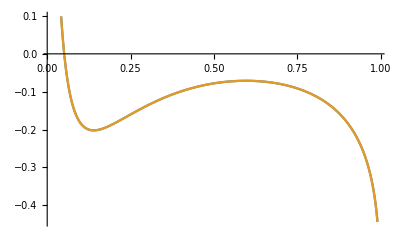

```mathematica
Plot[{fanalytic,%6},{u,0.01,0.99}]
```

```mathematica
NMaximize[{Abs[fanalytic-%6],u>0.0001,u<0.9999},u]
```

{2.47973×10^-14,{u→0.000109995}}

```mathematica
data1 = Table[{u,NIntegrate[f[p,u] ,{p,0,1}]},{u,0.001,0.999, 0.001}];
```

```mathematica
data2 = Table[{u,NIntegrate[f[p,u] ,{p,0,1}]},{u,0.001,0.999, 0.0005}];
```

```mathematica
data3 = Table[{u,NIntegrate[f[p,u] ,{p,0,1}]},{u,1.1,5.1, 1}]
```

{{1.1,-0.297332+0.494003 ⅈ},{2.1,3.55675+0.705025 ⅈ},{3.1,12.0752-6.97046 ⅈ},{4.1,22.4884-28.5715 ⅈ},{5.1,31.274-68.8754 ⅈ}}

```mathematica
data4 = Table[{u,NIntegrate[f[p,u] ,{p,0,1}]},{u,-0.1,-1.1, -1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0917813}. NIntegrate obtained -2088.4-3483.46 ⅈ and 2184.44 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.525375}. NIntegrate obtained -53914.3+4921.65 ⅈ and 25060. for the integral and error estimates.

{{-0.1,-2088.4-3483.46 ⅈ},{-1.1,-53914.3+4921.65 ⅈ}}

```mathematica
points1000 = Sort[RandomReal[{0.001,0.999},1000]];
```

```mathematica
data5 = Map[{#,NIntegrate[f[p,#] ,{p,0,1}]}&,points1000]
```

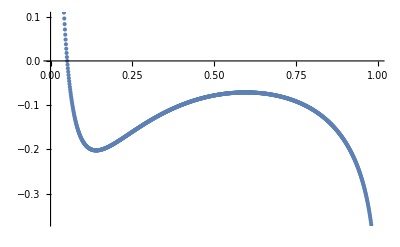

```mathematica
ListPlot[data1]
```

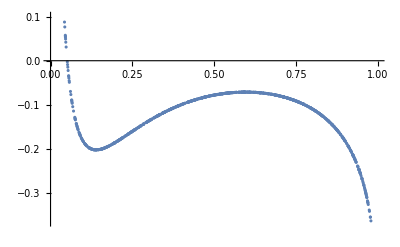

```mathematica
ListPlot[data5]
```

A union of uniform points and log uniform around 0 and 1

```mathematica
unipoints[nu_,nl_] :=  Sort[Join[Table[1/(nu*2^i),{i,2,nl+1}],
Table[1-1/(nu*2^i),{i,2,nl+1}],
RandomSample[Table[i/(16*nu),{i,1,16*nu-1}],nu]]]
```

```mathematica
unipoints70 = unipoints[50,10];
unipoints200 = unipoints[150,25];
```

```mathematica
residualdata2 = data2 - Table[{0,analytic },{u,0.001,0.999, 0.0005}];
```

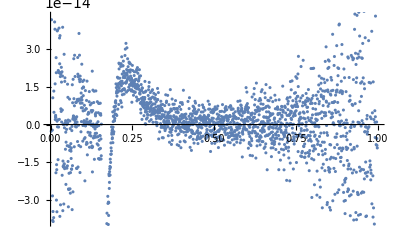

```mathematica
ListPlot[residualdata2]
```

```mathematica
data3 - Table[{0,analytic },{u,1.1,5.1,1}]
```

{{1.1,-1.34337×10^-14+0.989769 ⅈ},{2.1,1.10578×10^-13+1.90242 ⅈ},{3.1,-2.59348×10^-13-11.0846 ⅈ},{4.1,3.94351×10^-13-48.7715 ⅈ},{5.1,3.57403×10^-12-119.661 ⅈ}}

LinguisticAssistant

```mathematica
uvars = Variables[fanalytic]
```

{u,Log[-1+u],Log[u],PolyLog[2,1-u],PolyLog[2,(-1+u)/u],PolyLog[2,u],PolyLog[3,(-1+u)/u],PolyLog[3,u],PolyLog[3,u/(-1+u)]}

```mathematica
vars = Prepend[Drop[uvars,1],1]
```

{1,Log[-1+u],Log[u],PolyLog[2,1-u],PolyLog[2,(-1+u)/u],PolyLog[2,u],PolyLog[3,(-1+u)/u],PolyLog[3,u],PolyLog[3,u/(-1+u)]}

```mathematica
var2 = Flatten[Table[u^k1 Log[u]^k2 Log[1-u]^k3, {k1,0,2}, {k2,0,2},{k3,0,2}]]
```

{1,Log[1-u],Log[1-u]^2,Log[u],Log[1-u] Log[u],Log[1-u]^2 Log[u],Log[u]^2,Log[1-u] Log[u]^2,Log[1-u]^2 Log[u]^2,u,u Log[1-u],u Log[1-u]^2,u Log[u],u Log[1-u] Log[u],u Log[1-u]^2 Log[u],u Log[u]^2,u Log[1-u] Log[u]^2,u Log[1-u]^2 Log[u]^2,u^2,u^2 Log[1-u],u^2 Log[1-u]^2,u^2 Log[u],u^2 Log[1-u] Log[u],u^2 Log[1-u]^2 Log[u],u^2 Log[u]^2,u^2 Log[1-u] Log[u]^2,u^2 Log[1-u]^2 Log[u]^2}

```mathematica
allfns :=DeleteDuplicates[Flatten[Outer[Times,var2 ,vars]]];
```

```mathematica
fit1 := Fit[data1,allfns,u];
```

```mathematica
residual = fit1 - analytic;
```

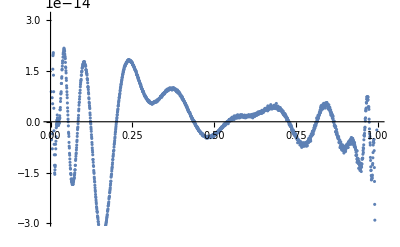

```mathematica
ListPlot[Table[{u,residual},{u,0.001,0.999,0.0005}]]
```

```mathematica
Table[residual,{u,1.1,5.1,1}]
```

{0.0503695+0.841345 ⅈ,-1.23549+1.73328 ⅈ,-5.74567-8.2108 ⅈ,-14.2157-35.4158 ⅈ,-25.6935-83.6046 ⅈ}

```mathematica
fit2 := Fit[data2,allfns,u];
```

```mathematica
residual2 = fit2 - analytic;
```

```mathematica
ListPlot[Table[{u,residual2},{u,0.001,0.999,0.0005}]]
```

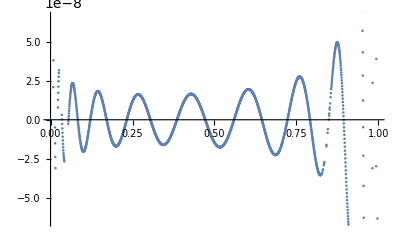

-Graphics-

```mathematica
Table[{u,residual},{u,0.001,0.999,0.05}]
```

{{0.001,2.17781×10^-11-3.22415×10^-15 ⅈ},{0.051,7.10543×10^-15+2.42861×10^-16 ⅈ},{0.101,1.74305×10^-14+4.03323×10^-16 ⅈ},{0.151,-3.26406×10^-14+9.41955×10^-16 ⅈ},{0.201,-2.22045×10^-16-2.55872×10^-17 ⅈ},{0.251,1.67644×10^-14-7.14272×10^-16 ⅈ},{0.301,5.96745×10^-15+9.45424×10^-17 ⅈ},{0.351,9.08995×10^-15+2.53703×10^-16 ⅈ},{0.401,7.31359×10^-15+6.11924×10^-16 ⅈ},{0.451,-2.08167×10^-15+3.67761×10^-16 ⅈ},{0.501,-3.77476×10^-15+2.25514×10^-17 ⅈ},{0.551,6.10623×10^-16-2.1684×10^-19 ⅈ},{0.601,1.52656×10^-15+2.64979×10^-16 ⅈ},{0.651,3.31679×10^-15+6.37511×10^-16 ⅈ},{0.701,4.10783×10^-15+2.57173×10^-16 ⅈ},{0.751,-4.76008×10^-15+3.43909×10^-16 ⅈ},{0.801,-2.80331×10^-15+7.76289×10^-17 ⅈ},{0.851,4.2466×10^-15-1.83881×10^-16 ⅈ},{0.901,-8.16014×10^-15+7.2338×10^-16 ⅈ},{0.951,-1.25455×10^-14+8.32667×10^-16 ⅈ}}

```mathematica
Table[{u,residual2},{u,0.001,0.999,0.05}]
```

{{0.001,3.7362×10^-9+1.5026×10^-9 ⅈ},{0.051,-1.28484×10^-8+1.2966×10^-10 ⅈ},{0.101,-2.03818×10^-8+8.51514×10^-11 ⅈ},{0.151,1.67529×10^-8-5.82077×10^-11 ⅈ},{0.201,-1.69457×10^-8+6.82121×10^-11 ⅈ},{0.251,1.23655×10^-8+1.72804×10^-11 ⅈ},{0.301,2.3756×10^-9-1.81899×10^-11 ⅈ},{0.351,-1.55633×10^-8+8.00355×10^-11 ⅈ},{0.401,8.90577×10^-9+4.36557×10^-11 ⅈ},{0.451,1.14669×10^-8-1.81899×10^-11 ⅈ},{0.501,-1.49776×10^-8+4.36557×10^-11 ⅈ},{0.551,-5.53337×10^-9+7.63976×10^-11 ⅈ},{0.601,1.94959×10^-8+7.27596×10^-12 ⅈ},{0.651,-5.22414×10^-9+2.18279×10^-11 ⅈ},{0.701,-1.843×10^-8+9.09495×10^-11 ⅈ},{0.751,2.54731×10^-8+2.91038×10^-11 ⅈ},{0.801,-1.52686×10^-8+1.45519×10^-11 ⅈ},{0.851,6.59929×10^-9+1.01863×10^-10 ⅈ},{0.901,-3.49246×10^-8+7.27596×10^-12 ⅈ},{0.951,6.98274×10^-8-3.63798×10^-12 ⅈ}}

```mathematica
Table[{u,residual2},{u,1.1,5.1,1}]
```

{{1.1,207581.+350075. ⅈ},{2.1,4.56743×10^6-4.8247×10^6 ⅈ},{3.1,4.73201×10^6-3.45745×10^7 ⅈ},{4.1,-1.51232×10^7-1.06838×10^8 ⅈ},{5.1,-7.91689×10^7-2.37931×10^8 ⅈ}}

Now do the fit with the exact functions appearing in the analytic result.

```mathematica
FromCoefficientRules[Map[#[[1]] -> 1&,CoefficientRules[fanalytic ,uvars]],uvars] /. Plus->List
```

{1,u,u^2,{ⅈ π,Log[u]},{ⅈ π u,u Log[u]},{ⅈ π u^2,u^2 Log[u]},{-π^2,Log[u]^2},{-π^2 u,u Log[u]^2},{-π^2 u^2,u^2 Log[u]^2},{-ⅈ π^3,Log[u]^3},{-ⅈ π^3 u,u Log[u]^3},{-ⅈ π^3 u^2,u^2 Log[u]^3},Log[u],u Log[u],u^2 Log[u],{ⅈ π Log[u],Log[u]^2},{ⅈ π u Log[u],u Log[u]^2},{ⅈ π u^2 Log[u],u^2 Log[u]^2},{-π^2 Log[u],Log[u]^3},{-π^2 u Log[u],u Log[u]^3},{-π^2 u^2 Log[u],u^2 Log[u]^3},Log[u]^2,u Log[u]^2,u^2 Log[u]^2,{ⅈ π Log[u]^2,Log[u]^3},{ⅈ π u Log[u]^2,u Log[u]^3},{ⅈ π u^2 Log[u]^2,u^2 Log[u]^3},Log[u]^3,u Log[u]^3,u^2 Log[u]^3,{π^2/6,PolyLog[2,-u]},{(π^2 u)/6,u PolyLog[2,-u]},{PolyLog[2,-1/u],π^2/6},{u PolyLog[2,-1/u],(π^2 u)/6},{u^2 PolyLog[2,-1/u],(π^2 u^2)/6},{ⅈ π PolyLog[2,-1/u],1/6 π^2 Log[u]},{ⅈ π u PolyLog[2,-1/u],1/6 π^2 u Log[u]},{ⅈ π u^2 PolyLog[2,-1/u],1/6 π^2 u^2 Log[u]},{Log[u] PolyLog[2,-1/u],1/6 π^2 Log[u]},{u Log[u] PolyLog[2,-1/u],1/6 π^2 u Log[u]},{u^2 Log[u] PolyLog[2,-1/u],1/6 π^2 u^2 Log[u]},Log[u] PolyLog[2,u],u Log[u] PolyLog[2,u],u^2 Log[u] PolyLog[2,u],{PolyLog[3,-1/u],Zeta[3]},{u PolyLog[3,-1/u],u Zeta[3]},{u^2 PolyLog[3,-1/u],u^2 Zeta[3]},PolyLog[3,u],u PolyLog[3,u],u^2 PolyLog[3,u],{PolyLog[3,-u],Zeta[3]},{u PolyLog[3,-u],u Zeta[3]},{u^2 PolyLog[3,-u],u^2 Zeta[3]}}

```mathematica
newvars = Map[FromCoefficientRules[{#[[1]] -> 1},uvars]&,CoefficientRules[fanalytic ,uvars]]
```

{u^2 Log[-1+u]^3,u^2 Log[-1+u]^2 Log[u],u^2 Log[-1+u]^2,u^2 Log[-1+u] Log[u]^2,u^2 Log[-1+u] Log[u],u^2 Log[-1+u] PolyLog[2,(-1+u)/u],u^2 Log[-1+u],u^2 Log[u]^3,u^2 Log[u]^2,u^2 Log[u] PolyLog[2,(-1+u)/u],u^2 Log[u] PolyLog[2,u],u^2 Log[u],u^2 PolyLog[2,(-1+u)/u],u^2 PolyLog[3,(-1+u)/u],u^2 PolyLog[3,u],u^2 PolyLog[3,u/(-1+u)],u^2,u Log[-1+u]^3,u Log[-1+u]^2 Log[u],u Log[-1+u]^2,u Log[-1+u] Log[u]^2,u Log[-1+u] Log[u],u Log[-1+u] PolyLog[2,(-1+u)/u],u Log[-1+u],u Log[u]^3,u Log[u]^2,u Log[u] PolyLog[2,(-1+u)/u],u Log[u] PolyLog[2,u],u Log[u],u PolyLog[2,1-u],u PolyLog[2,(-1+u)/u],u PolyLog[3,(-1+u)/u],u PolyLog[3,u],u PolyLog[3,u/(-1+u)],u,Log[-1+u]^3,Log[-1+u]^2 Log[u],Log[-1+u]^2,Log[-1+u] Log[u]^2,Log[-1+u] Log[u],Log[-1+u] PolyLog[2,(-1+u)/u],Log[-1+u],Log[u]^3,Log[u]^2,Log[u] PolyLog[2,(-1+u)/u],Log[u] PolyLog[2,u],Log[u],PolyLog[2,1-u],PolyLog[2,(-1+u)/u],PolyLog[3,(-1+u)/u],PolyLog[3,u],PolyLog[3,u/(-1+u)],1}

```mathematica
newvars /. {Log[-1+u]->Log[1-u],PolyLog[n_,(-1+u)/u]->PolyLog[n,(-1+u)/u]
```

{u^2 Log[1-u]^3,u^2 Log[1-u]^2 Log[u],u^2 Log[1-u]^2,u^2 Log[1-u] Log[u]^2,u^2 Log[1-u] Log[u],u^2 Log[1-u] PolyLog[2,(-1+u)/u],u^2 Log[1-u],u^2 Log[u]^3,u^2 Log[u]^2,u^2 Log[u] PolyLog[2,(-1+u)/u],u^2 Log[u] PolyLog[2,u],u^2 Log[u],u^2 PolyLog[2,(-1+u)/u],u^2 PolyLog[3,(-1+u)/u],u^2 PolyLog[3,u],u^2 PolyLog[3,u/(-1+u)],u^2,u Log[1-u]^3,u Log[1-u]^2 Log[u],u Log[1-u]^2,u Log[1-u] Log[u]^2,u Log[1-u] Log[u],u Log[1-u] PolyLog[2,(-1+u)/u],u Log[1-u],u Log[u]^3,u Log[u]^2,u Log[u] PolyLog[2,(-1+u)/u],u Log[u] PolyLog[2,u],u Log[u],u PolyLog[2,1-u],u PolyLog[2,(-1+u)/u],u PolyLog[3,(-1+u)/u],u PolyLog[3,u],u PolyLog[3,u/(-1+u)],u,Log[1-u]^3,Log[1-u]^2 Log[u],Log[1-u]^2,Log[1-u] Log[u]^2,Log[1-u] Log[u],Log[1-u] PolyLog[2,(-1+u)/u],Log[1-u],Log[u]^3,Log[u]^2,Log[u] PolyLog[2,(-1+u)/u],Log[u] PolyLog[2,u],Log[u],PolyLog[2,1-u],PolyLog[2,(-1+u)/u],PolyLog[3,(-1+u)/u],PolyLog[3,u],PolyLog[3,u/(-1+u)],1}

Can we make an orthogonal basis?

Find linear dependencies in this basis.

```mathematica
A = Map[newvars /. u->#&, points1000];
```

```mathematica
Dimensions[A]
```

{1000,53}

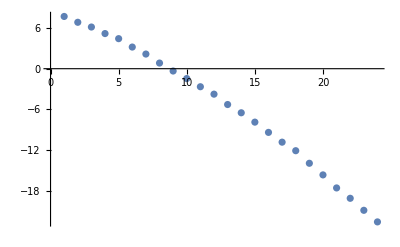

```mathematica
ListPlot[Log[SingularValueList[A]]]
```

```mathematica
Aext = Table[newvars,{u,-100.5,100.5}];
```

```mathematica
SingularValueList[Aext]
```

{1.70824×10^7,4.26625×10^6,140214.,35726.1,3163.74,1491.19,339.648,126.314,68.1923,37.1532,21.7691,15.5978,7.02936,2.88022,1.40406,0.431853,0.229878,0.0660124,0.0261652,0.00690755,0.00232937,0.000565835,0.000185965,0.0000353277,9.41526×10^-6,2.18749×10^-6,8.46939×10^-7}

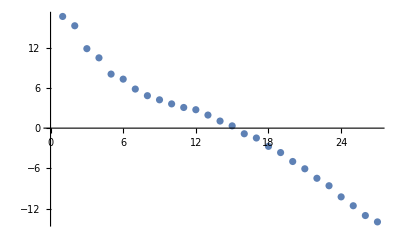

```mathematica
ListPlot[Log[SingularValueList[Aext]]]
```

```mathematica
Aextp60 = Table[N[newvars,60],{u,-100 - 1/2,100 + 1/2}];
```

```mathematica
Dimensions[Aextp60]
```

{202,53}

```mathematica
nullext = NullSpace[Aext];
```

```mathematica
N[newvars[[1]] /. u->100+1/2, 60]
```

983219.013206576757719645666045335733013314959817198097030167

```mathematica
n1000 = NullSpace[A];
```

```mathematica
n200 = NullSpace[ Map[newvars /. u->#&, Take[points1000,200]] ];
```

```mathematica
Dimensions[n1000]
```

{29,53}

```mathematica
nullvars = nullext . newvars;
```

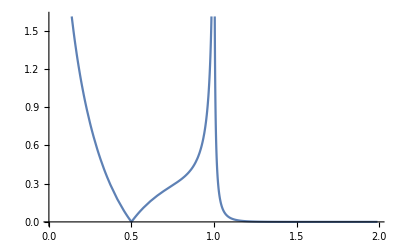

```mathematica
Plot[Abs[nullvars[[1]]],{u,0.01,1.99}]
```

```mathematica
newfit1 := Fit[data1,newvars,u];
```

```mathematica
newresidual = newfit1 - analytic;
```

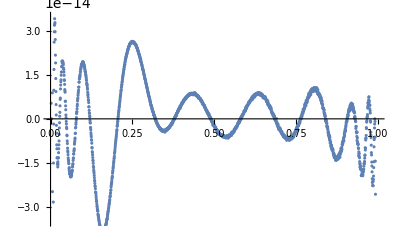

```mathematica
ListPlot[Table[{u,newresidual},{u,0.001,0.999,0.0005}]]
```

```mathematica
Table[newresidual,{u,1.1,5.1,1}]
```

{0.00472025+0.0160455 ⅈ,1.06735-0.195495 ⅈ,5.6913-7.84254 ⅈ,15.9973-30.9508 ⅈ,33.7179-75.9619 ⅈ}

```mathematica
newfit3 := Fit[Join[data5,data3],newvars,u];
```

```mathematica
newresidual3 = newfit3 - analytic;
```

```mathematica
Table[{u,newresidual3},{u,0.0005,0.999,0.01}]
```

{{0.0005,0.00001677-0.000376899 ⅈ},{0.0105,3.4488×10^-9-7.35963×10^-9 ⅈ},{0.0205,-3.86717×10^-9+1.32786×10^-8 ⅈ},{0.0305,1.35697×10^-8-5.1914×10^-8 ⅈ},{0.0405,-5.63887×10^-10+5.62432×10^-9 ⅈ},{0.0505,-1.21199×10^-8+3.97231×10^-8 ⅈ},{0.0605,-9.39053×10^-9+2.62808×10^-8 ⅈ},{0.0705,5.95719×10^-10-4.01633×10^-9 ⅈ},{0.0805,9.08449×10^-9-2.56623×10^-8 ⅈ},{0.0905,1.18205×10^-8-3.01006×10^-8 ⅈ},{0.1005,8.82847×10^-9-2.046×10^-8 ⅈ},{0.1105,2.44881×10^-9-4.27099×10^-9 ⅈ},{0.1205,-4.45471×10^-9+1.13796×10^-8 ⅈ},{0.1305,-9.65429×10^-9+2.19006×10^-8 ⅈ},{0.1405,-1.19844×10^-8+2.54659×10^-8 ⅈ},{0.1505,-1.11568×10^-8+2.24827×10^-8 ⅈ},{0.1605,-7.77254×10^-9+1.47265×10^-8 ⅈ},{0.1705,-2.78851×10^-9+4.51109×10^-9 ⅈ},{0.1805,2.65754×10^-9-5.79894×10^-9 ⅈ},{0.1905,7.53062×10^-9-1.44064×10^-8 ⅈ},{0.2005,1.10504×10^-8-2.00234×10^-8 ⅈ},{0.2105,1.26902×10^-8-2.21698×10^-8 ⅈ},{0.2205,1.23437×10^-8-2.08092×10^-8 ⅈ},{0.2305,1.01627×10^-8-1.65091×10^-8 ⅈ},{0.2405,6.49288×10^-9-1.00626×10^-8 ⅈ},{0.2505,1.87447×10^-9-2.47383×10^-9 ⅈ},{0.2605,-3.11957×10^-9+5.26052×10^-9 ⅈ},{0.2705,-7.83984×10^-9+1.226×10^-8 ⅈ},{0.2805,-1.18043×10^-8+1.77824×10^-8 ⅈ},{0.2905,-1.45601×10^-8+2.13186×10^-8 ⅈ},{0.3005,-1.58489×10^-8+2.26428×10^-8 ⅈ},{0.3105,-1.55687×10^-8+2.17042×10^-8 ⅈ},{0.3205,-1.37479×10^-8+1.87501×10^-8 ⅈ},{0.3305,-1.05501×10^-8+1.40717×10^-8 ⅈ},{0.3405,-6.2837×10^-9+8.22183×10^-9 ⅈ},{0.3505,-1.33605×10^-9+1.70985×10^-9 ⅈ},{0.3605,3.87354×10^-9-4.85306×10^-9 ⅈ},{0.3705,8.88303×10^-9-1.09503×10^-8 ⅈ},{0.3805,1.32941×10^-8-1.60653×10^-8 ⅈ},{0.3905,1.67083×10^-8-1.98124×10^-8 ⅈ},{0.4005,1.88484×10^-8-2.19734×10^-8 ⅈ},{0.4105,1.95332×10^-8-2.23808×10^-8 ⅈ},{0.4205,1.86792×10^-8-2.10348×10^-8 ⅈ},{0.4305,1.633×10^-8-1.81208×10^-8 ⅈ},{0.4405,1.26347×10^-8-1.38643×10^-8 ⅈ},{0.4505,7.83257×10^-9-8.57108×10^-9 ⅈ},{0.4605,2.27919×10^-9-2.67755×10^-9 ⅈ},{0.4705,-3.61433×10^-9+3.36513×10^-9 ⅈ},{0.4805,-9.42782×10^-9+9.11314×10^-9 ⅈ},{0.4905,-1.47047×10^-8+1.41335×10^-8 ⅈ},{0.5005,-1.90139×10^-8+1.80989×10^-8 ⅈ},{0.5105,-2.20043×10^-8+2.06637×10^-8 ⅈ},{0.5205,-2.33867×10^-8+2.16714×10^-8 ⅈ},{0.5305,-2.29775×10^-8+2.1013×10^-8 ⅈ},{0.5405,-2.07274×10^-8+1.87392×10^-8 ⅈ},{0.5505,-1.66838×10^-8+1.5003×10^-8 ⅈ},{0.5605,-1.10867×10^-8+1.00372×10^-8 ⅈ},{0.5705,-4.22551×10^-9+4.19095×10^-9 ⅈ},{0.5805,3.40697×10^-9-2.08092×10^-9 ⅈ},{0.5905,1.13014×10^-8-8.36008×10^-9 ⅈ},{0.6005,1.88356×10^-8-1.41445×10^-8 ⅈ},{0.6105,2.54258×10^-8-1.90375×10^-8 ⅈ},{0.6205,3.04772×10^-8-2.25955×10^-8 ⅈ},{0.6305,3.34448×10^-8-2.44909×10^-8 ⅈ},{0.6405,3.39905×10^-8-2.45673×10^-8 ⅈ},{0.6505,3.18541×10^-8-2.27737×10^-8 ⅈ},{0.6605,2.70065×10^-8-1.9194×10^-8 ⅈ},{0.6705,1.96796×10^-8-1.40535×10^-8 ⅈ},{0.6805,1.03346×10^-8-7.79983×10^-9 ⅈ},{0.6905,-3.37877×10^-10-9.02219×10^-10 ⅈ},{0.7005,-1.13905×10^-8+5.99539×10^-9 ⅈ},{0.7105,-2.17628×10^-8+1.21872×10^-8 ⅈ},{0.7205,-3.0298×10^-8+1.70912×10^-8 ⅈ},{0.7305,-3.58345×10^-8+2.00889×10^-8 ⅈ},{0.7405,-3.73677×10^-8+2.07729×10^-8 ⅈ},{0.7505,-3.42145×10^-8+1.88847×10^-8 ⅈ},{0.7605,-2.60911×10^-8+1.45155×10^-8 ⅈ},{0.7705,-1.33225×10^-8+8.01447×10^-9 ⅈ},{0.7805,3.06682×10^-9+3.27418×10^-11 ⅈ},{0.7905,2.12895×10^-8-8.41464×10^-9 ⅈ},{0.8005,3.88509×10^-8-1.61381×10^-8 ⅈ},{0.8105,5.26616×10^-8-2.18461×10^-8 ⅈ},{0.8205,5.94518×10^-8-2.43344×10^-8 ⅈ},{0.8305,5.6174×10^-8-2.27155×10^-8 ⅈ},{0.8405,4.08118×10^-8-1.66747×10^-8 ⅈ},{0.8505,1.32691×10^-8-6.71025×10^-9 ⅈ},{0.8605,-2.36196×10^-8+5.61522×10^-9 ⅈ},{0.8705,-6.32617×10^-8+1.78261×10^-8 ⅈ},{0.8805,-9.48748×10^-8+2.65463×10^-8 ⅈ},{0.8905,-1.04527×10^-7+2.83944×10^-8 ⅈ},{0.9005,-7.80269×10^-8+2.10566×10^-8 ⅈ},{0.9105,-7.78573×10^-9+4.98039×10^-9 ⅈ},{0.9205,9.59458×10^-8-1.50176×10^-8 ⅈ},{0.9305,1.88868×10^-7-2.90556×10^-8 ⅈ},{0.9405,1.77581×10^-7-2.49138×10^-8 ⅈ},{0.9505,-7.22744×10^-8+1.91721×10^-9 ⅈ},{0.9605,-6.44571×10^-7+3.02625×10^-8 ⅈ},{0.9705,-1.27583×10^-6+6.55245×10^-9 ⅈ},{0.9805,-8.97134×10^-7-5.52814×10^-8 ⅈ},{0.9905,3.50219×10^-7+5.4195×10^-8 ⅈ}}

```mathematica
Table[{u,newresidual3},{u,1.001,1.999,0.01}]
```

```mathematica
Log[-((-1+u) u)]//. {1-2u+2u^2 -> z1,Log[-((-1+u)u)]->z2}
```

z2

```mathematica
A = Map[newvars /. {Log[-1+u] -> Log[1-u]}/. u->#&, unipoints70];
```

```mathematica
Dimensions[A]
```

{70,53}

```mathematica
A100 = N[A,100];
```

```mathematica
A5 = RowReduce[A,Modulus->5];
```

RowReduce::nmod: {«1»} is not valid modulo 5.

```mathematica
A100rat = Rationalize[A100,0];
```

```mathematica
A100row = RowReduce[A100rat];
```